```mathematica
(*
1. Найти приближенные значения производных первого и второго порядков функции
f (x) в точке x0, используя:
а)функцию D системы Mathematica;
б)формулы численного дифференцирования 
yi`≈1/h*(∆yi−1/2*∆^2yi+1/3*∆^3yi) 
и yi`≈1/h^2*(∆^2yi−∆^3yi)
для шага h1=0,1 и шага h2=0,01.
1.1. f(x) = tgln3x, x0 = 2.13
*)
f[x_] = Tan[Log[3*x]];
x0=2.13;
df1[x_]=f'[x];
df2[x_]=f''[x];

df1[x0]
df2[x0]
```

5.98241

-22.0576

```mathematica
h1=0.1;
h=h1;
deltaY=f[x0+h]-f[x0];
deltaY1=f[x0+2h]-f[x0+h];
deltaY2=f[x0+3h]-f[x0+2h];
del2y0=deltaY1-deltaY; 
del2y1=deltaY2-deltaY1; 
del3y0=del2y1-del2y0; 

dy1=N[1/h*(deltaY-1/2*del2y0+1/3*del3y0)]
d2y1=N[1/h^2*(del2y0-del3y0)]
```

5.89013

-18.3234

```mathematica
h2 = 0.01;
h=h2;
deltaY=f[x0+h]-f[x0];
deltaY1=f[x0+2h]-f[x0+h];
deltaY2=f[x0+3h]-f[x0+2h];
del2y0=deltaY1-deltaY; 
del2y1=deltaY2-deltaY1; 
del3y0=del2y1-del2y0; 

dy2=N[1/h*(deltaY-1/2*del2y0+1/3*del3y0)]
d2y2=N[1/h^2*(del2y0-del3y0)]
```

5.9822

-21.9788

```mathematica
(*Вывод: при уменьшении показателя h точность нахождения 1ой и 2ой производных повышается*)
```

```mathematica
(*2. а) Вычислить с помощью формулы второго порядка точности и составить таблицу
приближенных значений yi' производной функции f (x) на отрезке[−1,3] с шагом h=0,2.
б) Изобразить на одном чертеже (на отрезке[−1,3]) график функции f'(x),
полученной с помощью функции D пакета Mathematica,и точки (xi,y'i), соответствующие
приближенным значениям производной, найденным в пункте а.
2.1.f (x)=sh(ln ch x).
*)
f[x_] = Sinh[Log[Cosh[x]]];
a= -1;
b= 3;
h=0.2;
df[x_]=D[f[x],x];
table = Table[{xi,N[(f[xi+h]-f[xi-h])/(2*h)]},{xi,-1,3,h}];
TableForm[table]
```

-1. | -0.835793
-0.8 | -0.69139
-0.6 | -0.542088
-0.4 | -0.37772
-0.2 | -0.195081
0. | 0.
0.2 | 0.195081
0.4 | 0.37772
0.6 | 0.542088
0.8 | 0.69139
1. | 0.835793
1.2 | 0.988688
1.4 | 1.1639
1.6 | 1.37461
1.8 | 1.63363
2. | 1.95415
2.2 | 2.35075
2.4 | 2.84035
2.6 | 3.44321
2.8 | 4.18383
3. | 5.09213

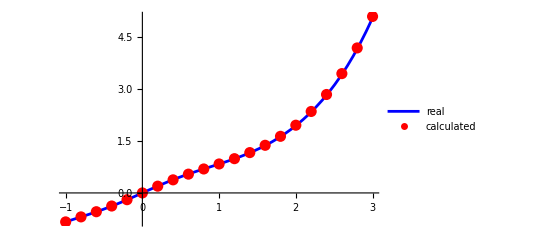

```mathematica
Show[Plot[df[x],{x,-1,3},
PlotStyle->Blue,
PlotLegends->{"real"}],
ListPlot[Table[{xi,N[(f[xi+h]-f[xi-h])/(2*h)]},{xi,-1,3,h}],
PlotStyle->{Red,PointSize[0.02]},
PlotLegends->{"calculated"}],PlotRange->All]
```

```mathematica
(*
Вывод: способ получает достаточно точные значения функции, однако лишь в точках а не везде.
этот способ может быть выгоден когда нужно быстро посчитать производную функции в точке
*)
(*
3. Вычислить определенный интеграл:
3.1
а) по формуле средних прямоугольников
*)
a = 0.7;
b = 1.5;
g[x_] = Power[x^2+6,1/3]/(3x+Sqrt[x^2+0.6]);
n1 = 8;
integral18=(b-a)/n1*Sum[g[a+(i-1)*(b-a)/n1+(b-a)/(2n1)],{i,1,n1}]
n2 = 10;
integral110=(b-a)/n2*Sum[g[a+(i-1)*(b-a)/n2+(b-a)/(2n2)],{i,1,n2}]
rich1=integral110+(integral110-integral18)/((n2/n1)^2-1)
```

0.343792

0.343864

0.343993

```mathematica
(*
b)по формуле трапеций
*)
integral28 = (b-a)/n1*(g[a]/2+Sum[g[a+i*(b-a)/n1],{i,1,n1-1}]+g[b]/2)
integral210 = (b-a)/n2*(g[a]/2+Sum[g[a+i*(b-a)/n2],{i,1,n2-1}]+g[b]/2)
rich2 = integral210+(integral210-integral28)/((n2/n1)^2-1)
```

0.344396

0.344251

0.343993

```mathematica
true = NIntegrate[g[x],{x,a,b}]
```

0.343993

```mathematica
Abs[integral18-true]
Abs[integral110-true]
Abs[rich1-true]

Abs[integral28-true]
Abs[integral210-true]
Abs[rich2-true]
```

0.000201302

0.000128951

3.28172×10^-7

0.000403044

0.000258084

3.75397×10^-7

```mathematica
(*Формула средних квадратов точнее чем формула трапеций по всем 3м показателям.
При увеличении количства точек точность формулы возарстает.
Уточнение интеграла по Ричардсону дает самый максимальный результат для любой формулы*)
(*
4. Вычислить определенный интеграл от таблично заданной функции по формуле
Симпсона (парабол) для разбиений отрезка интегрирования на 8 и на 16 частей.
*)
t={{1.2,0.1823},{1.3,0.2624},{1.4,0.3365},{1.5,0.4055},{1.6,0.4700},
{1.7,0.5306},{1.8,0.5878},{1.9,0.6419},{2.0,0.6931},{2.1,0.7419},
{2.2,0.7885},{2.3,0.8329},{2.4,0.8755},{2.5,0.9163},{2.6,0.9555},
{2.7,0.9933},{2.8,1.0296}};
ys=t[[All,2]];
n1=4;
h1=(2.8-1.2)/(2*n1);
ys1=ys[[1;; ;;2]]; 
integral8=h1/3*(ys1[[1]]+ys1[[-1]]+4*Sum[ys1[[2*i]],{i,1,n1}]+2*Sum[ys1[[2*i-1]],{i,2,n1}])
n2=8;
h2=(2.8-1.2)/(2*n2); 
ys2=ys;
integral16=h2/3*(ys2[[1]]+ys2[[-1]]+4*Sum[ys2[[2*i]],{i,1,n2}]+2*Sum[ys2[[2*i-1]],{i,2,n2}])
```

1.06415

1.06416

{{1.2,0.1823},{1.3,0.2624},{1.4,0.3365},{1.5,0.4055},{1.6,0.47},{1.7,0.5306},{1.8,0.5878},{1.9,0.6419},{2.,0.6931},{2.1,0.7419},{2.2,0.7885},{2.3,0.8329},{2.4,0.8755},{2.5,0.9163},{2.6,0.9555},{2.7,0.9933},{2.8,1.0296}}

```mathematica
(*
5. Вычислить определенный интеграл с помощью квадратурной формулы Гаусса с n
узлами.
*)
f[x_]=Log[2 x]/(4 x+1);
a=1.1;b=2;
n=4;
Pn=LegendreP[n,x]
```

1/8 (3-30 x^2+35 x^4)

```mathematica
tt=x/.NSolve[Pn==0,x]

T=Table[tt[[j]]^k,{k,0,n-1},{j,1,n}];
MatrixForm[T]
```

{-0.861136,-0.339981,0.339981,0.861136}

(1. | 1. | 1. | 1.
-0.861136 | -0.339981 | 0.339981 | 0.861136
0.741556 | 0.115587 | 0.115587 | 0.741556
-0.638581 | -0.0392974 | 0.0392974 | 0.638581)

```mathematica
B=Table[(1-(-1)^(k+1))/(k+1),{k,0,n-1}]

A=LinearSolve[T,B]
```

{2,0,2/3,0}

{0.347855,0.652145,0.652145,0.347855}

```mathematica
h=(b-a)/2;
c=(a+b)/2;

integral=h*Sum[A[[i]]*f[h*tt[[i]]+c],{i,1,n}]
```

0.139416

```mathematica
exact=NIntegrate[f[x],{x,a,b}]
Abs[integral-exact]
```

0.139416

4.41723×10^-8